# Catalan Numbers

Peter Cullen Burbery

I analyze several applications of Catalan numbers.

## Catalan Sequences

Find the 20th totally balanced binary sequence with five 1’s:

```mathematica
CatalanUnrank[5,20]
```

{0,0,1,0,1,0,1,1,0,1}

Find the number of totally balanced binary sequences with five 1's:

```mathematica
CatalanNumber[5]
```

42

Show the totally balanced binary sequences with five 1’s:

```mathematica
CatalanUnrank[5,#]&/@Range[0,CatalanNumber[5]-1]
```

{{0,0,0,0,0,1,1,1,1,1},{0,0,0,0,1,0,1,1,1,1},{0,0,0,0,1,1,0,1,1,1},{0,0,0,0,1,1,1,0,1,1},{0,0,0,0,1,1,1,1,0,1},{0,0,0,1,0,0,1,1,1,1},{0,0,0,1,0,1,0,1,1,1},{0,0,0,1,0,1,1,0,1,1},{0,0,0,1,0,1,1,1,0,1},{0,0,0,1,1,0,0,1,1,1},{0,0,0,1,1,0,1,0,1,1},{0,0,0,1,1,0,1,1,0,1},{0,0,0,1,1,1,0,0,1,1},{0,0,0,1,1,1,0,1,0,1},{0,0,1,0,0,0,1,1,1,1},{0,0,1,0,0,1,0,1,1,1},{0,0,1,0,0,1,1,0,1,1},{0,0,1,0,0,1,1,1,0,1},{0,0,1,0,1,0,0,1,1,1},{0,0,1,0,1,0,1,0,1,1},{0,0,1,0,1,0,1,1,0,1},{0,0,1,0,1,1,0,0,1,1},{0,0,1,0,1,1,0,1,0,1},{0,0,1,1,0,0,0,1,1,1},{0,0,1,1,0,0,1,0,1,1},{0,0,1,1,0,0,1,1,0,1},{0,0,1,1,0,1,0,0,1,1},{0,0,1,1,0,1,0,1,0,1},{0,1,0,0,0,0,1,1,1,1},{0,1,0,0,0,1,0,1,1,1},{0,1,0,0,0,1,1,0,1,1},{0,1,0,0,0,1,1,1,0,1},{0,1,0,0,1,0,0,1,1,1},{0,1,0,0,1,0,1,0,1,1},{0,1,0,0,1,0,1,1,0,1},{0,1,0,0,1,1,0,0,1,1},{0,1,0,0,1,1,0,1,0,1},{0,1,0,1,0,0,0,1,1,1},{0,1,0,1,0,0,1,0,1,1},{0,1,0,1,0,0,1,1,0,1},{0,1,0,1,0,1,0,0,1,1},{0,1,0,1,0,1,0,1,0,1}}

## Grouping Symbols

Find all sets of 3 parentheses that are balanced:

```mathematica
AllBalancedGroupingSymbols[{"(",")"},3]
```

{((())),(()()),(())(),()(()),()()()}

### Parentheses ()

```mathematica
AllBalancedGroupingSymbols[{"(",")"},4]
```

{(((()))),((()())),((())()),((()))(),(()(())),(()()()),(()())(),(())(()),(())()(),()((())),()(()()),()(())(),()()(()),()()()()}

### Angle Brackets ⟨⟩

```mathematica
AllBalancedGroupingSymbols[{"⟨","⟩"},4]
```

{⟨⟨⟨⟨⟩⟩⟩⟩,⟨⟨⟨⟩⟨⟩⟩⟩,⟨⟨⟨⟩⟩⟨⟩⟩,⟨⟨⟨⟩⟩⟩⟨⟩,⟨⟨⟩⟨⟨⟩⟩⟩,⟨⟨⟩⟨⟩⟨⟩⟩,⟨⟨⟩⟨⟩⟩⟨⟩,⟨⟨⟩⟩⟨⟨⟩⟩,⟨⟨⟩⟩⟨⟩⟨⟩,⟨⟩⟨⟨⟨⟩⟩⟩,⟨⟩⟨⟨⟩⟨⟩⟩,⟨⟩⟨⟨⟩⟩⟨⟩,⟨⟩⟨⟩⟨⟨⟩⟩,⟨⟩⟨⟩⟨⟩⟨⟩}

### Square Brackets []

```mathematica
AllBalancedGroupingSymbols[{"[","]"},4]
```

{[[[[]]]],[[[][]]],[[[]][]],[[[]]][],[[][[]]],[[][][]],[[][]][],[[]][[]],[[]][][],[][[[]]],[][[][]],[][[]][],[][][[]],[][][][]}

### Curly Brackets {}

```mathematica
AllBalancedGroupingSymbols[{"{","}"},4]
```

{{{{{}}}},{{{}{}}},{{{}}{}},{{{}}}{},{{}{{}}},{{}{}{}},{{}{}}{},{{}}{{}},{{}}{}{},{}{{{}}},{}{{}{}},{}{{}}{},{}{}{{}},{}{}{}{}}

### Floor Brackets ⌊⌋

```mathematica
AllBalancedGroupingSymbols[{"⌊","⌋"},4]
```

{⌊⌊⌊⌊⌋⌋⌋⌋,⌊⌊⌊⌋⌊⌋⌋⌋,⌊⌊⌊⌋⌋⌊⌋⌋,⌊⌊⌊⌋⌋⌋⌊⌋,⌊⌊⌋⌊⌊⌋⌋⌋,⌊⌊⌋⌊⌋⌊⌋⌋,⌊⌊⌋⌊⌋⌋⌊⌋,⌊⌊⌋⌋⌊⌊⌋⌋,⌊⌊⌋⌋⌊⌋⌊⌋,⌊⌋⌊⌊⌊⌋⌋⌋,⌊⌋⌊⌊⌋⌊⌋⌋,⌊⌋⌊⌊⌋⌋⌊⌋,⌊⌋⌊⌋⌊⌊⌋⌋,⌊⌋⌊⌋⌊⌋⌊⌋}

### Ceiling Brackets ⌈⌉

```mathematica
AllBalancedGroupingSymbols[{"⌈","⌉"},4]
```

{⌈⌈⌈⌈⌉⌉⌉⌉,⌈⌈⌈⌉⌈⌉⌉⌉,⌈⌈⌈⌉⌉⌈⌉⌉,⌈⌈⌈⌉⌉⌉⌈⌉,⌈⌈⌉⌈⌈⌉⌉⌉,⌈⌈⌉⌈⌉⌈⌉⌉,⌈⌈⌉⌈⌉⌉⌈⌉,⌈⌈⌉⌉⌈⌈⌉⌉,⌈⌈⌉⌉⌈⌉⌈⌉,⌈⌉⌈⌈⌈⌉⌉⌉,⌈⌉⌈⌈⌉⌈⌉⌉,⌈⌉⌈⌈⌉⌉⌈⌉,⌈⌉⌈⌉⌈⌈⌉⌉,⌈⌉⌈⌉⌈⌉⌈⌉}

### Double Square Brackets ⟦⟧]

```mathematica
AllBalancedGroupingSymbols[{"⟦","⟧"},4]
```

{⟦⟦⟦⟦⟧⟧⟧⟧,⟦⟦⟦⟧⟦⟧⟧⟧,⟦⟦⟦⟧⟧⟦⟧⟧,⟦⟦⟦⟧⟧⟧⟦⟧,⟦⟦⟧⟦⟦⟧⟧⟧,⟦⟦⟧⟦⟧⟦⟧⟧,⟦⟦⟧⟦⟧⟧⟦⟧,⟦⟦⟧⟧⟦⟦⟧⟧,⟦⟦⟧⟧⟦⟧⟦⟧,⟦⟧⟦⟦⟦⟧⟧⟧,⟦⟧⟦⟦⟧⟦⟧⟧,⟦⟧⟦⟦⟧⟧⟦⟧,⟦⟧⟦⟧⟦⟦⟧⟧,⟦⟧⟦⟧⟦⟧⟦⟧}

### Bracketing Bars ||

```mathematica
AllBalancedGroupingSymbols[{"|","|"},4]
```

{||||||||,||||||||,||||||||,||||||||,||||||||,||||||||,||||||||,||||||||,||||||||,||||||||,||||||||,||||||||,||||||||,||||||||}

### Bracketing Bars ‖‖

```mathematica
AllBalancedGroupingSymbols[{"‖","‖"},4]
```

{‖‖‖‖‖‖‖‖,‖‖‖‖‖‖‖‖,‖‖‖‖‖‖‖‖,‖‖‖‖‖‖‖‖,‖‖‖‖‖‖‖‖,‖‖‖‖‖‖‖‖,‖‖‖‖‖‖‖‖,‖‖‖‖‖‖‖‖,‖‖‖‖‖‖‖‖,‖‖‖‖‖‖‖‖,‖‖‖‖‖‖‖‖,‖‖‖‖‖‖‖‖,‖‖‖‖‖‖‖‖,‖‖‖‖‖‖‖‖}

### String Template <*…*> symbols

```mathematica
AllBalancedGroupingSymbols[{"<*","|*>"},4]
```

{<*<*<*<*|*>|*>|*>|*>,<*<*<*|*><*|*>|*>|*>,<*<*<*|*>|*><*|*>|*>,<*<*<*|*>|*>|*><*|*>,<*<*|*><*<*|*>|*>|*>,<*<*|*><*|*><*|*>|*>,<*<*|*><*|*>|*><*|*>,<*<*|*>|*><*<*|*>|*>,<*<*|*>|*><*|*><*|*>,<*|*><*<*<*|*>|*>|*>,<*|*><*<*|*><*|*>|*>,<*|*><*<*|*>|*><*|*>,<*|*><*|*><*<*|*>|*>,<*|*><*|*><*|*><*|*>}

### Association Template <*…*> symbols

```mathematica
AllBalancedGroupingSymbols[{"<|","|>"},4]
```

{<|<|<|<||>|>|>|>,<|<|<||><||>|>|>,<|<|<||>|><||>|>,<|<|<||>|>|><||>,<|<||><|<||>|>|>,<|<||><||><||>|>,<|<||><||>|><||>,<|<||>|><|<||>|>,<|<||>|><||><||>,<||><|<|<||>|>|>,<||><|<||><||>|>,<||><|<||>|><||>,<||><||><|<||>|>,<||><||><||><||>}

## Mountain Range

I made a function that will make all mountain ranges named DyckPaths:

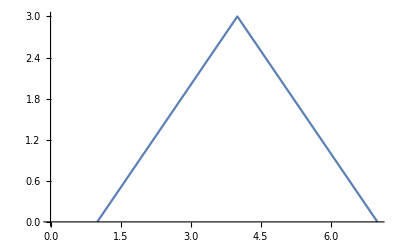
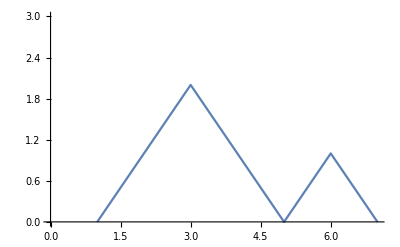
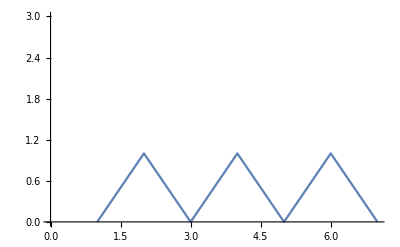
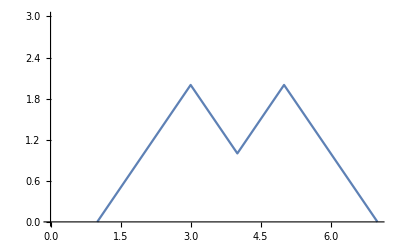
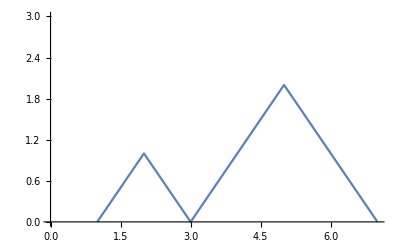
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |

```mathematica
Multicolumn[DyckPaths[3]]
```

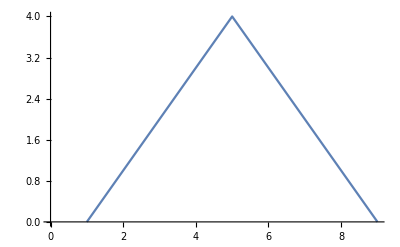
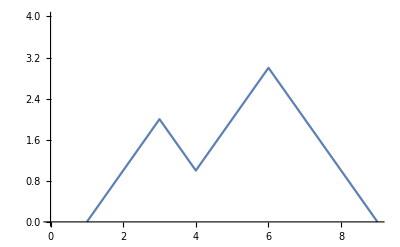
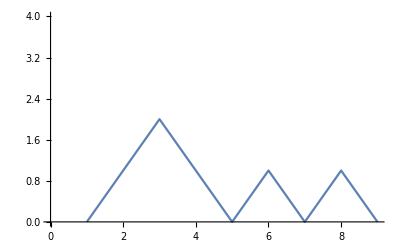
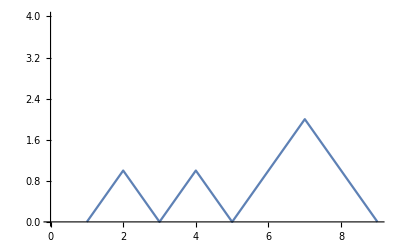
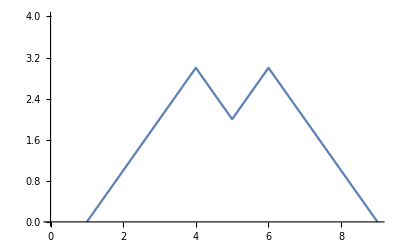
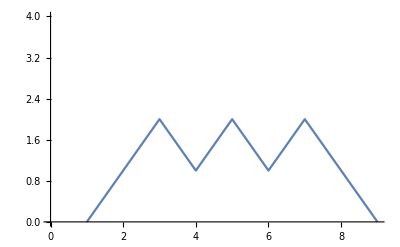
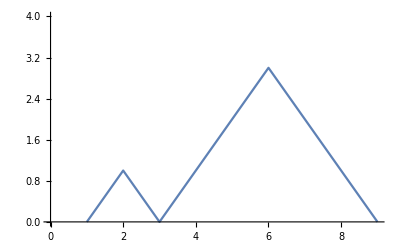
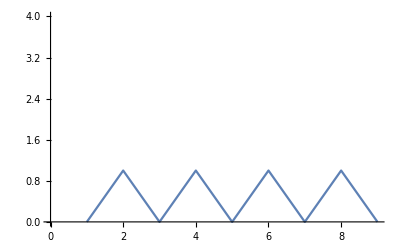
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- |

```mathematica
Multicolumn[DyckPaths[4]]
```

## Walks above or below the diagonal

I made a function that plots all walks above or below the diagonal.

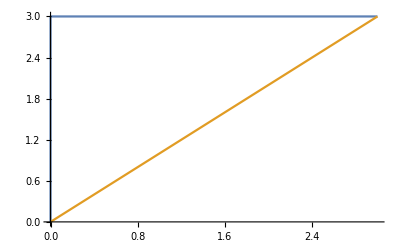
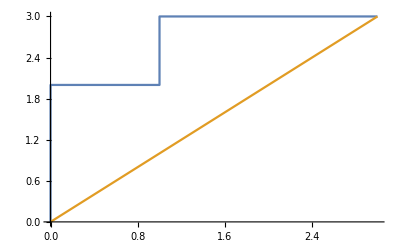
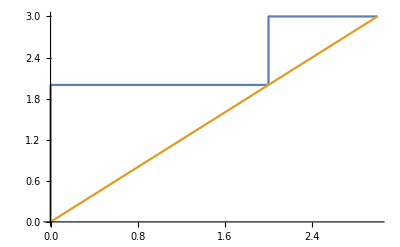
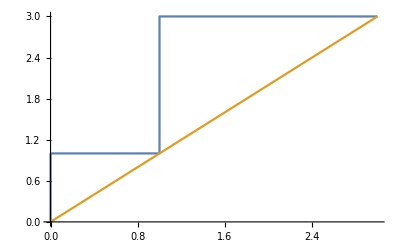
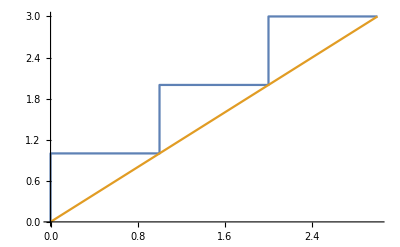
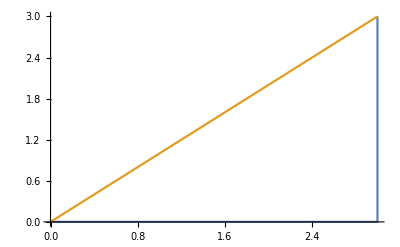
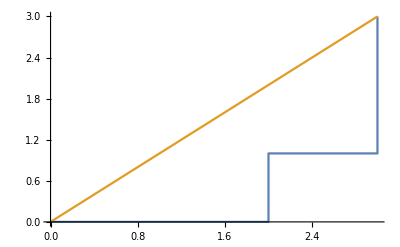
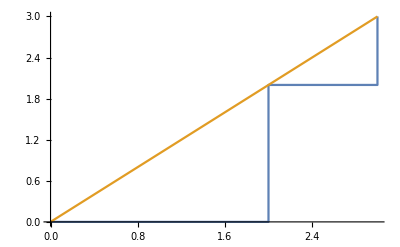

```mathematica
DiagonalWalkPlot[3,{1,1}]
```

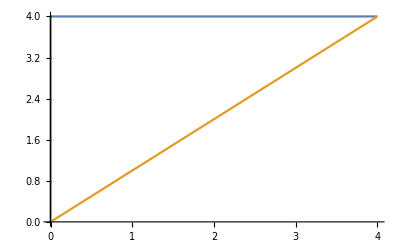
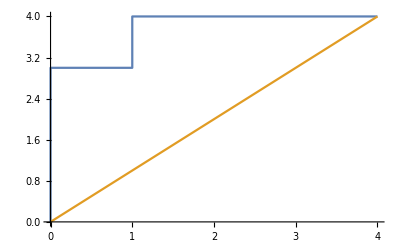
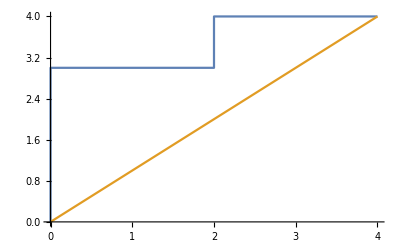
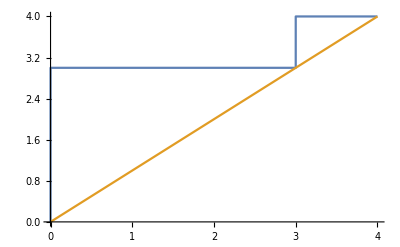
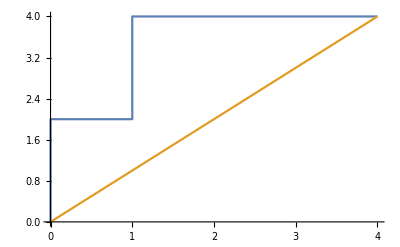
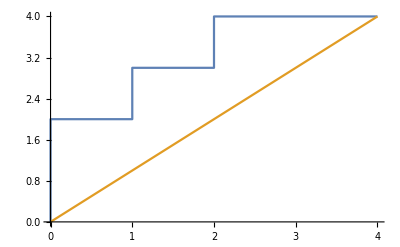
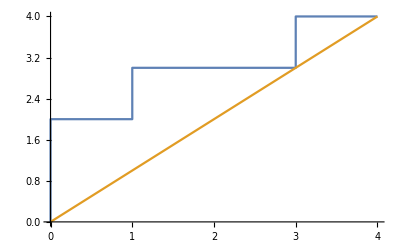
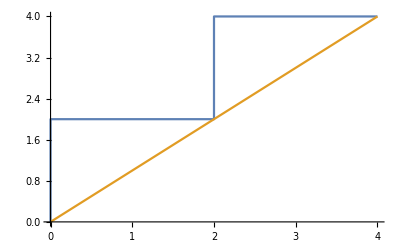

```mathematica
DiagonalWalkPlot[4,{1,1}]
```

## Parenthesized Expressions

I made another function that calculates the parenthesized expressions with a certain number of variables.

```mathematica
ParenthesizedExpressions[4,{b,c,d,f}]
```

{b⊕(c⊕(d⊕f)),b⊕((c⊕d)⊕f),(b⊕c)⊕(d⊕f),(b⊕(c⊕d))⊕f,((b⊕c)⊕d)⊕f}

```mathematica
ParenthesizedExpressions[5,{b,c,d,f,h}]
```

{b⊕(c⊕(d⊕(f⊕h))),b⊕(c⊕((d⊕f)⊕h)),b⊕((c⊕d)⊕(f⊕h)),b⊕((c⊕(d⊕f))⊕h),b⊕(((c⊕d)⊕f)⊕h),(b⊕c)⊕(d⊕(f⊕h)),(b⊕c)⊕((d⊕f)⊕h),(b⊕(c⊕d))⊕(f⊕h),((b⊕c)⊕d)⊕(f⊕h),(b⊕(c⊕(d⊕f)))⊕h,(b⊕((c⊕d)⊕f))⊕h,((b⊕c)⊕(d⊕f))⊕h,((b⊕(c⊕d))⊕f)⊕h,(((b⊕c)⊕d)⊕f)⊕h}

## Full Binary Trees

I made a function to list all full binary trees with n leaves.

```mathematica
FullBinaryTrees[4]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
FullBinaryTrees[5]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Regular Polygon Triangulations

Catalan numbers are also related to triangulations of regular polygons:

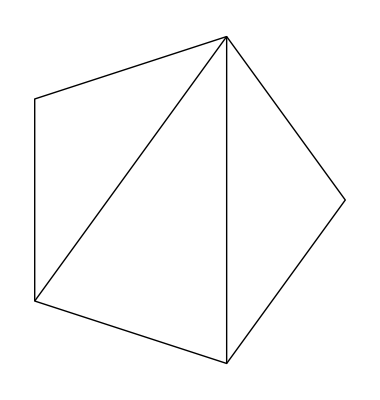
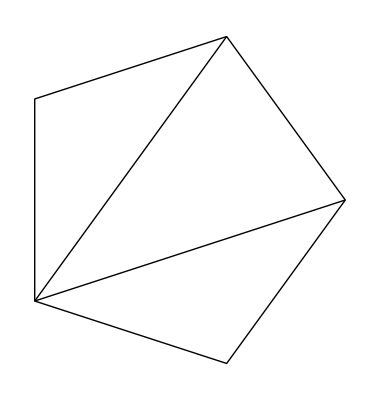
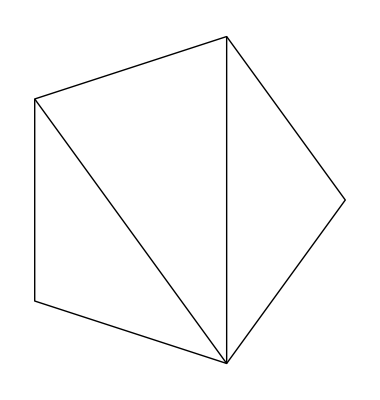
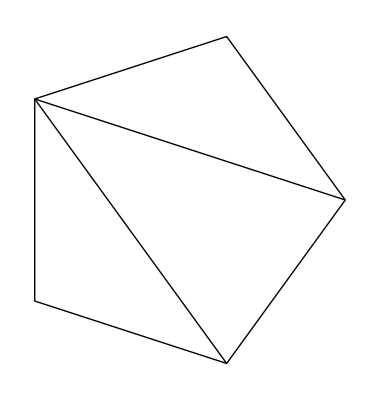
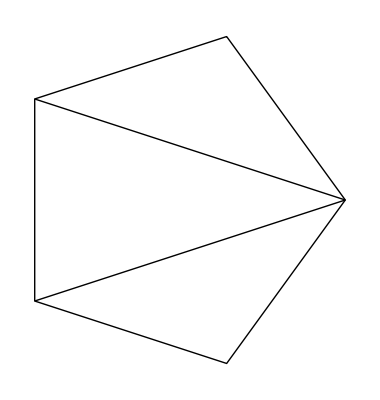

```mathematica
FindRegularPolygonTriangulations[5]
```

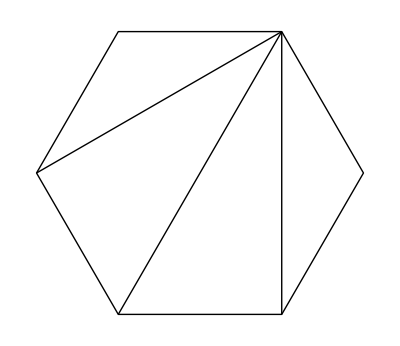
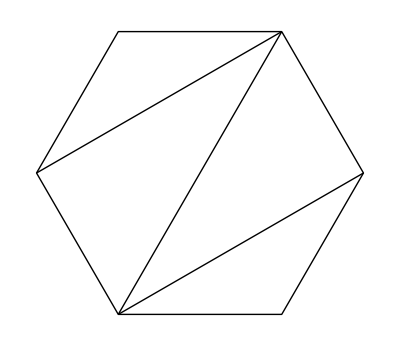
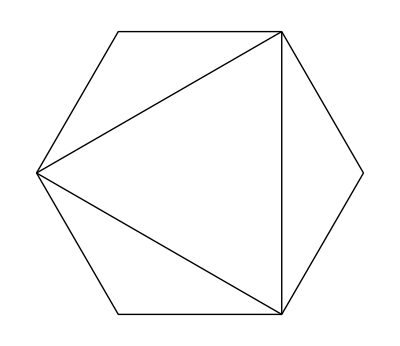
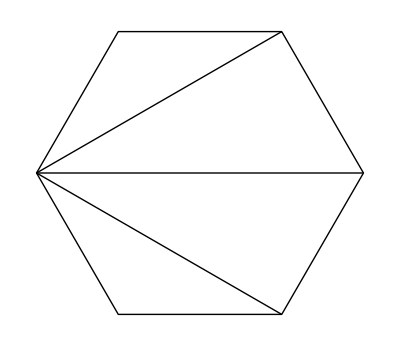
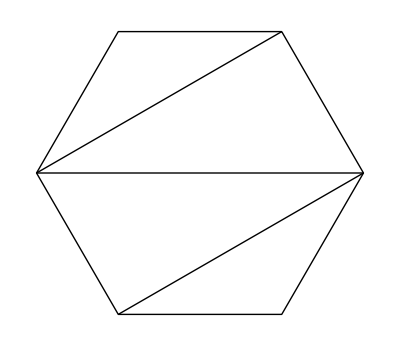
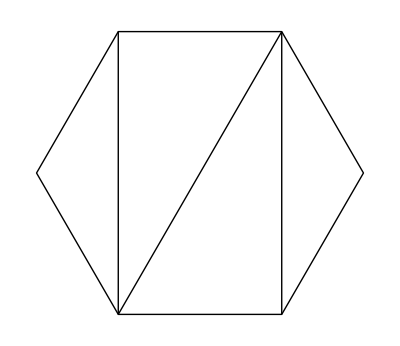
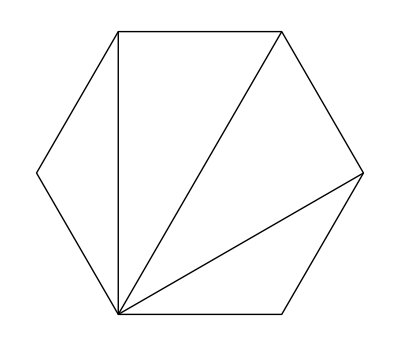
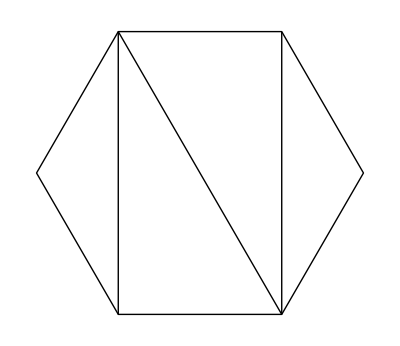

```mathematica
FindRegularPolygonTriangulations[6]
```

## Solving Puzzles

These puzzles are from Brilliant‘s wiki page on Catalan numbers.

## Restricted random walks:

A man walks n blocks north and n blocks west of his residence. Every day he has 2n blocks to walk. How many routes are possible if he never crosses the diagonal line from home to office?

Make a plot:

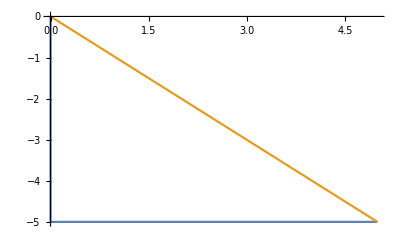
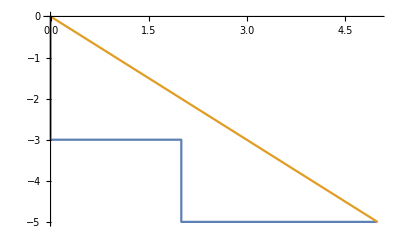
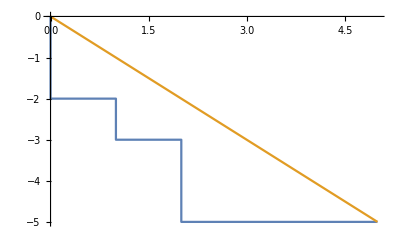
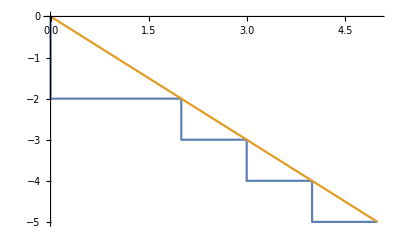
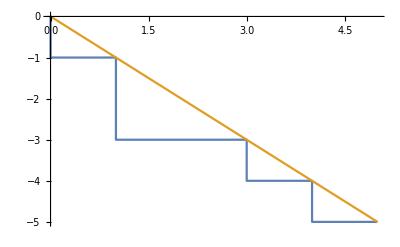
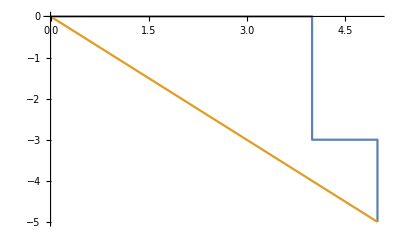
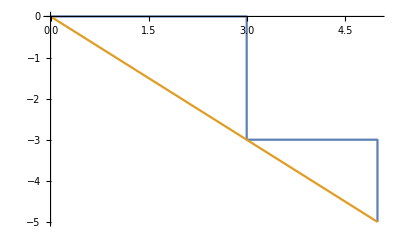
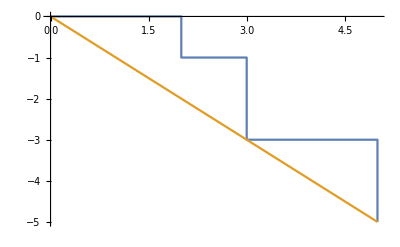
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |

```mathematica
Multicolumn@DiagonalWalkPlot[5,{1,-1}]
```

Count the walks:

```mathematica
Length[DiagonalWalkPlot[5,{1,-1}]]
```

84

Write the answer:

```mathematica
StringTemplate["There are <*Length[#1]*> routes possible if he never crosses the diagonal line from his home to his office."][DiagonalWalkPlot[5,{1,-1}]]
```

There are 84 routes possible if he never crosses the diagonal line from his home to his office.

## Binary Trees:

A rooted binary tree is a tree with one root node, where each node has either zero or two branches descending from it. A node is internal if it has two nodes coming from it. How many rooted binary trees are there with n internal nodes?

Make a table of the # of full binary trees:

```mathematica
Table[Length[FullBinaryTrees[t]],{t,2,9}]
```

{1,2,5,14,42,132,429,1430}

```mathematica
FindSequenceFunction[Table[Length[FullBinaryTrees[t]],{t,2,9}],n]
```

CatalanNumber[n]

Write the answer:

```mathematica
StringTemplate["There are <* ToString@TraditionalForm[#] *> rooted binary trees with n internal nodes."][FindSequenceFunction[Table[Length[FullBinaryTrees[t]],{t,2,9}],n]]
```

There are n rooted binary trees with n internal nodes.

## Applications in Combinatorics

This section is from the Wikipedia article on Catalan numbers.

There are many counting problems in combinatorics whose solution is given by the Catalan numbers. The book Enumerative Combinatorics: Volume 2 by combinatorialist Richard P. Stanley contains a set of exercises which describe 66 different interpretations of the Catalan numbers. Following are some examples, with illustrations of the cases C3 = 5 and C4 = 14.

C_n is the number of Dyck words[2] of length 2n. A Dyck word is a string consisting of n S’s and n T’s such that no initial segment of the string has more T’s than S’s. For example, the following are the Dyck words of length 6:

```mathematica
AllBalancedGroupingSymbols[{"S","T"},3]
```

{SSSTTT,SSTSTT,SSTTST,STSSTT,STSTST}

Re-interpreting the symbol S as an open parenthesis and T as a close parenthesis, C_n counts the number of expressions containing n pairs of parentheses which are correctly matched:

```mathematica
AllBalancedGroupingSymbols[{"(",")"},3]
```

{((())),(()()),(())(),()(()),()()()}

C_n is the number of different ways n + 1 factors can be completely parenthesized (or the number of ways of associating n applications of a binary operator, as in the matrix chain multiplication problem). For n = 3, for example, we have the following five different parenthesizations of four factors:

I don't like to use the variable's a, e, i, o, or u in math so although the Wikipedia article uses the variables a,b,c,d, I use only consonants and no vowels. The reason is vowels often have special meanings like e for ⅇ, lim_(t->0) (1+t)^(1/t), i for ⅈ √-1, and so on. O is used for Big O notation like O(n log n) for expressing asymptotic behavior in series and computer programs.

```mathematica
ParenthesizedExpressions[4,{b,c,d,f}]
```

{b⊕(c⊕(d⊕f)),b⊕((c⊕d)⊕f),(b⊕c)⊕(d⊕f),(b⊕(c⊕d))⊕f,((b⊕c)⊕d)⊕f}

Successive applications of a binary operator can be represented in terms of a full binary tree, with each correctly matched bracketing describing an internal node. It follows that C_n is the number of full binary trees with n + 1 leaves, or, equivalently, with a total of n internal nodes:

```mathematica
FullBinaryTrees[4]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

A convex polygon with n + 2 sides can be cut into triangles by connecting vertices with non-crossing line segments (a form of polygon triangulation). The number of triangles formed is n and the number of different ways that this can be achieved is C_n. The following hexagons illustrate the case n = 4:

```mathematica
FindRegularPolygonTriangulations[4+2]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

C_n is the number of ways to form a “mountain range” with n upstrokes and n downstrokes that all stay above a horizontal line. The mountain range interpretation is that the mountains will never go below the horizon.

```mathematica
DyckPaths[0]//Multicolumn
```

-Graphics-

```mathematica
DyckPaths[1]//Multicolumn
```

-Graphics-

```mathematica
DyckPaths[2]//Multicolumn
```

-Graphics- | -Graphics-

```mathematica
DyckPaths[3]//Multicolumn
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |

```mathematica
CatalanUnrank[3,#]&/@Range[0,CatalanNumber[3]-1]
```

{{0,0,0,1,1,1},{0,0,1,0,1,1},{0,0,1,1,0,1},{0,1,0,0,1,1},{0,1,0,1,0,1}}

```mathematica
DyckWords[n_,start_,end_]:=StringJoin[(CatalanUnrank[3,#]/.{0->start,1->end})]&/@Range[0,CatalanNumber[3]-1]
```

```mathematica
DyckWords[3,"S","T"]
```

{SSSTTT,SSTSTT,SSTTST,STSSTT,STSTST}

```mathematica
DyckWords[3,"(",")"]
```

{((())),(()()),(())(),()(()),()()()}

```mathematica
AllBalancedGroupingSymbols[{"(",")"},3]
```

{((())),(()()),(())(),()(()),()()()}

```mathematica
AllBalancedGroupingSymbols[{"(",")"},3]==DyckWords[3,"(",")"]
```

True

```mathematica
AllBalancedGroupingSymbols[{"S","T"},3]
```

{SSSTTT,SSTSTT,SSTTST,STSSTT,STSTST}

```mathematica
CatalanUnrank[4,#]&/@Range[0,CatalanNumber[4]-1]
```

{{0,0,0,0,1,1,1,1},{0,0,0,1,0,1,1,1},{0,0,0,1,1,0,1,1},{0,0,0,1,1,1,0,1},{0,0,1,0,0,1,1,1},{0,0,1,0,1,0,1,1},{0,0,1,0,1,1,0,1},{0,0,1,1,0,0,1,1},{0,0,1,1,0,1,0,1},{0,1,0,0,0,1,1,1},{0,1,0,0,1,0,1,1},{0,1,0,0,1,1,0,1},{0,1,0,1,0,0,1,1},{0,1,0,1,0,1,0,1}}

```mathematica
DiagonalWalkPlot[2,{1,-1}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
DataForDiagonalWalkPlot//ClearAll
DataForDiagonalWalkPlot[n_,{horizontaldirectionsign_,
verticaldirectionsign_}]:=First[Function[sign,({Prepend[
Accumulate[(sign (CatalanUnrank[n,#1]/.{0->-1}))
/. {-1->{0,verticaldirectionsign},1->{horizontaldirectionsign,0}}],
{0,0}]}&)/@Range[0,CatalanNumber[n]-1]]/@{1}]
```

```mathematica
DataForDiagonalWalkPlot[3,{1,1}]
```

{{{{0,0},{0,1},{0,2},{0,3},{1,3},{2,3},{3,3}}},{{{0,0},{0,1},{0,2},{1,2},{1,3},{2,3},{3,3}}},{{{0,0},{0,1},{0,2},{1,2},{2,2},{2,3},{3,3}}},{{{0,0},{0,1},{1,1},{1,2},{1,3},{2,3},{3,3}}},{{{0,0},{0,1},{1,1},{1,2},{2,2},{2,3},{3,3}}}}

```mathematica
(CatalanUnrank[3,#]/.{0->{1,0},1->{0,1}})&/@Range[0,CatalanNumber[3]-1]
```

{{{1,0},{1,0},{1,0},{0,1},{0,1},{0,1}},{{1,0},{1,0},{0,1},{1,0},{0,1},{0,1}},{{1,0},{1,0},{0,1},{0,1},{1,0},{0,1}},{{1,0},{0,1},{1,0},{1,0},{0,1},{0,1}},{{1,0},{0,1},{1,0},{0,1},{1,0},{0,1}}}

```mathematica
First[(CatalanUnrank[3,#]/.{0->{1,0},1->{0,1}})&/@Range[0,CatalanNumber[3]-1]]
```

{{1,0},{1,0},{1,0},{0,1},{0,1},{0,1}}

```mathematica
Accumulate[First[(CatalanUnrank[3,#]/.{0->{1,0},1->{0,1}})&/@Range[0,CatalanNumber[3]-1]]]
```

{{1,0},{2,0},{3,0},{3,1},{3,2},{3,3}}

```mathematica
Accumulate[First[(CatalanUnrank[4,#]/.{0->{1,0},1->{0,1}})&/@Range[0,CatalanNumber[4]-1]]]
```

{{1,0},{2,0},{3,0},{4,0},{4,1},{4,2},{4,3},{4,4}}

```mathematica
Prepend[Accumulate[First[(CatalanUnrank[4,#]/.{0->{1,0},1->{0,1}})&/@Range[0,CatalanNumber[4]-1]]],{0,0}]
```

{{0,0},{1,0},{2,0},{3,0},{4,0},{4,1},{4,2},{4,3},{4,4}}

```mathematica
ListLinePlot[Prepend[Accumulate[First[(CatalanUnrank[4,#]/.{0->{1,0},1->{0,1}})&/@Range[0,CatalanNumber[4]-1]]],{0,0}]]
```

-Graphics-

```mathematica
ListLinePlot[Prepend[Accumulate[Part[(CatalanUnrank[4,#]/.{0->{1,0},1->{0,1}})&/@Range[0,CatalanNumber[4]-1],2]],{0,0}]]
```

-Graphics-

```mathematica
Prepend[Accumulate[First[(CatalanUnrank[4,#]/.{0->{1,0},1->{0,1}})&/@Range[0,CatalanNumber[4]-1]]],{0,0}]
```

{{0,0},{1,0},{2,0},{3,0},{4,0},{4,1},{4,2},{4,3},{4,4}}

```mathematica
Partition[Prepend[Accumulate[First[(CatalanUnrank[4,#]/.{0->{1,0},1->{0,1}})&/@Range[0,CatalanNumber[4]-1]]],{0,0}],2]
```

{{{0,0},{1,0}},{{2,0},{3,0}},{{4,0},{4,1}},{{4,2},{4,3}}}

```mathematica
Map[Last,Partition[Prepend[Accumulate[First[(CatalanUnrank[4,#]/.{0->{1,0},1->{0,1}})&/@Range[0,CatalanNumber[4]-1]]],{0,0}],2],{2}]
```

{{0,0},{0,0},{0,1},{2,3}}

```mathematica
Accumulate[First[(CatalanUnrank[4,#]/.{0->{1,0},1->{0,1}})&/@Range[0,CatalanNumber[4]-1]]]
```

{{1,0},{2,0},{3,0},{4,0},{4,1},{4,2},{4,3},{4,4}}

```mathematica
Accumulate[Part[(CatalanUnrank[4,#]/.{0->{1,0},1->{0,1}})&/@Range[0,CatalanNumber[4]-1],2]]
```

{{1,0},{2,0},{3,0},{3,1},{4,1},{4,2},{4,3},{4,4}}

```mathematica
Accumulate[Part[(CatalanUnrank[4,#]/.{0->{1,0},1->{0,1}})&/@Range[0,CatalanNumber[4]-1],-1]]
```

{{1,0},{1,1},{2,1},{2,2},{3,2},{3,3},{4,3},{4,4}}

```mathematica
ListLinePlot[Prepend[Accumulate[Part[(CatalanUnrank[4,#]/.{0->{1,0},1->{0,1}})&/@Range[0,CatalanNumber[4]-1],-1]],{0,0}]]
```

-Graphics-